```mathematica
SetDirectory @ NotebookDirectory[];
<<PlotCustom.m
```

# PLATAFORMA DE STEWART

-Graphics-

## CINEMÁTICA

### PARÂMETROS CINEMÁTICOS

```mathematica
Subscript[R, base]=0.5;  (*Raio da base*)
Subscript[R, plat]=0.25; (*Raio da plataforma*)
Subscript[γ, b]=0; (*Distância angular entre juntas da base*)
Subscript[γ, p]=0; (*Distância angular entre juntas da plataforma*)
```

### PONTOS DA BASE E PLATAFORMA

```mathematica
Subscript[t, b][t_]= {x[t],y[t],z[t]}; (*Vetor origem base até origem plataforma*)

(*Matriz de rotação*)
Subscript[R, P] = {{Cos[ψ[t]]*Cos[θ[t]], Sin[ϕ[t]]*Sin[θ[t]]*Cos[ψ[t]]-Cos[ϕ[t]]*Sin[ψ[t]],Cos[ϕ[t]]*Sin[θ[t]]*Cos[ψ[t]]-Sin[ϕ[t]]*Sin[ψ[t]]},
{Sin[ψ[t]]*Cos[θ[t]], Sin[ϕ[t]]*Sin[θ[t]]*Sin[ψ[t]]+Cos[ϕ[t]]*Cos[ψ[t]], Cos[ϕ[t]]*Sin[θ[t]]*Sin[ψ[t]]-Sin[ϕ[t]]*Cos[ψ[t]]},
{-Sin[θ[t]], Sin[ϕ[t]]*Cos[θ[t]], Cos[ϕ[t]]*Cos[θ[t]]}};

(*Pontos da plataforma*)
Subscript[P, 1] = { -Cos[(π/6) - (Subscript[γ, p]/2)]*Subscript[R, plat],-Sin[(π/6) - (Subscript[γ, p]/2)]*Subscript[R, plat],0};
Subscript[P, 2] = {-Sin[Subscript[γ, p]/2]*Subscript[R, plat] ,Cos[Subscript[γ, p]/2]*Subscript[R, plat],0};
Subscript[P, 3] = {Sin[Subscript[γ, p]/2]*Subscript[R, plat],Cos[Subscript[γ, p]/2]*Subscript[R, plat],0};
Subscript[P, 4] = {Cos[(π/6) - (Subscript[γ, p]/2)]*Subscript[R, plat],-Sin[(π/6) - (Subscript[γ, p]/2)]*Subscript[R, plat],0};
Subscript[P, 5] = {Cos[(π/6) + (Subscript[γ, p]/2)]*Subscript[R, plat],-Sin[(π/6) + (Subscript[γ, p]/2)]*Subscript[R, plat],0};
Subscript[P, 6] = {-Cos[(π/6) + (Subscript[γ, p]/2)]*Subscript[R, plat],-Sin[(π/6) + (Subscript[γ, p]/2)]*Subscript[R, plat],0};

(*Pontos da base*)
Subscript[B, 1] ={-Cos[(π/6) - (Subscript[γ, b]/2)]*Subscript[R, base],Sin[(π/6) - (Subscript[γ, b]/2)]*Subscript[R, base],0};
Subscript[B, 2] ={-Cos[(π/6) + (Subscript[γ, b]/2)]*Subscript[R, base],Sin[(π/6) + (Subscript[γ, b]/2)]*Subscript[R, base],0};
Subscript[B, 3] = {Cos[(π/6) + (Subscript[γ, b]/2)]*Subscript[R, base],Sin[(π/6) + (Subscript[γ, b]/2)]*Subscript[R, base],0};
Subscript[B, 4] ={Cos[(π/6) - (Subscript[γ, b]/2)]*Subscript[R, base],Sin[(π/6) - (Subscript[γ, b]/2)]*Subscript[R, base],0};
Subscript[B, 5] ={Sin[Subscript[γ, b]/2]*Subscript[R, base],-Cos[Subscript[γ, b]/2]*Subscript[R, base],0};
Subscript[B, 6] ={-Sin[Subscript[γ, b]/2]*Subscript[R, base],-Cos[Subscript[γ, b]/2]*Subscript[R, base],0};
```

### CÁLCULO DO COMPRIMENTO DOS ATUADORES

```mathematica
(*Vetores que representam cada atuador*)
Subscript[S, 1]= Subscript[R, P] . Subscript[P, 1] + Subscript[t, b][t] - Subscript[B, 1];
Subscript[S, 2] =Subscript[R, P] . Subscript[P, 2] + Subscript[t, b][t] - Subscript[B, 2];
Subscript[S, 3] =Subscript[R, P] . Subscript[P, 3] + Subscript[t, b][t] - Subscript[B, 3];
Subscript[S, 4]= Subscript[R, P] . Subscript[P, 4] + Subscript[t, b][t] - Subscript[B, 4];
Subscript[S, 5]= Subscript[R, P] . Subscript[P, 5] + Subscript[t, b][t] - Subscript[B, 5];
Subscript[S, 6]= Subscript[R, P] . Subscript[P, 6] + Subscript[t, b][t] - Subscript[B, 6];

(*Comprimento de cada atuador*)
Subscript[L, 1]=Sqrt[(Subscript[S, 1][[1]])^2+(Subscript[S, 1][[2]])^2+(Subscript[S, 1][[3]])^2];
Subscript[L, 2]=Sqrt[(Subscript[S, 2][[1]])^2+(Subscript[S, 2][[2]])^2+(Subscript[S, 2][[3]])^2];
Subscript[L, 3]=Sqrt[(Subscript[S, 3][[1]])^2+(Subscript[S, 3][[2]])^2+(Subscript[S, 3][[3]])^2];
Subscript[L, 4]=Sqrt[(Subscript[S, 4][[1]])^2+(Subscript[S, 4][[2]])^2+(Subscript[S, 4][[3]])^2];
Subscript[L, 5]=Sqrt[(Subscript[S, 5][[1]])^2+(Subscript[S, 5][[2]])^2+(Subscript[S, 5][[3]])^2];
Subscript[L, 6]=Sqrt[(Subscript[S, 6][[1]])^2+(Subscript[S, 6][[2]])^2+(Subscript[S, 6][[3]])^2];
```

## DINÂMICA

### DEDUÇÃO DAS EQUAÇÕES DE MOVIMENTO

```mathematica
Subscript[R, ω] = {{Cos[ψ[t]]*Cos[θ[t]],-Sin[ψ[t]],0},{Cos[θ[t]]*Sin[ψ[t]],Cos[ψ[t]],0},{-Sin[ψ[t]],0,1}}; (*Matriz de rotação*)
ω[t_]={ϕ'[t],θ'[t],ψ'[t]}; (*Vetor velocidade angular*)
Subscript[bω, p] = Subscript[R, ω] . ω[t]//FullSimplify;(*Velocidade angular da plataforma referenciada à base*)
Subscript[bω, x]=Subscript[bω, p][[1]];
Subscript[bω, y]=Subscript[bω, p][[2]];
Subscript[bω, z]=Subscript[bω, p][[3]];
```

```mathematica
(*Vetores unitários dos atuadores*)
Subscript[s, 1]=Subscript[S, 1]/Subscript[L, 1];
Subscript[s, 2]=-Subscript[S, 2]/Subscript[L, 2];
Subscript[s, 3]=Subscript[S, 3] /Subscript[L, 3];
Subscript[s, 4]=-Subscript[S, 4]/Subscript[L, 4];
Subscript[s, 5]=Subscript[S, 5]/Subscript[L, 5];
Subscript[s, 6]=-Subscript[S, 6]/Subscript[L, 6];

(*Pontos da plataforma na coordenada da base*)
Subscript[bP, 1]=Subscript[R, P].Subscript[P, 1]+Subscript[t, b][t];
Subscript[bP, 2]=Subscript[R, P].Subscript[P, 2]+Subscript[t, b][t];
Subscript[bP, 3]=Subscript[R, P].Subscript[P, 3]+Subscript[t, b][t];
Subscript[bP, 4]=Subscript[R, P].Subscript[P, 4]+Subscript[t, b][t];
Subscript[bP, 5]=Subscript[R, P].Subscript[P, 5]+Subscript[t, b][t];
Subscript[bP, 6]=Subscript[R, P].Subscript[P, 6]+Subscript[t, b][t];

(*Produtos vetoriais Subscript[s, i] Λ Subscript[bP, i]*)
Subscript[vet, 1]=Cross[Subscript[bP, 1],Subscript[s, 1]];
Subscript[vet, 2]=Cross[Subscript[bP, 2],Subscript[s, 2]];
Subscript[vet, 3]=Cross[Subscript[bP, 3],Subscript[s, 3]];
Subscript[vet, 4]=Cross[Subscript[bP, 4],Subscript[s, 4]];
Subscript[vet, 5]=Cross[Subscript[bP, 5],Subscript[s, 5]];
Subscript[vet, 6]=Cross[Subscript[bP, 6],Subscript[s, 6]];

(*Matrix jacobiana*)
Subscript[bJ, p]=({{Subscript[s, 1][[1]],Subscript[s, 1][[2]],Subscript[s, 1][[3]],Subscript[vet, 1][[1]],Subscript[vet, 1][[2]],Subscript[vet, 1][[3]]},
{Subscript[s, 2][[1]],Subscript[s, 2][[2]],Subscript[s, 2][[3]],Subscript[vet, 2][[1]],Subscript[vet, 2][[2]],Subscript[vet, 2][[3]]},
{Subscript[s, 3][[1]],Subscript[s, 3][[2]],Subscript[s, 3][[3]],Subscript[vet, 3][[1]],Subscript[vet, 3][[2]],Subscript[vet, 3][[3]]},
{Subscript[s, 4][[1]],Subscript[s, 4][[2]],Subscript[s, 4][[3]],Subscript[vet, 4][[1]],Subscript[vet, 4][[2]],Subscript[vet, 4][[3]]},
{Subscript[s, 5][[1]],Subscript[s, 5][[2]],Subscript[s, 5][[3]],Subscript[vet, 5][[1]],Subscript[vet, 5][[2]],Subscript[vet, 5][[3]]},
{Subscript[s, 6][[1]],Subscript[s, 6][[2]],Subscript[s, 6][[3]],Subscript[vet, 6][[1]],Subscript[vet, 6][[2]],Subscript[vet, 6][[3]]}})*9.244/2.3; (*Correções para compensar os erros das forças*)
```

```mathematica
Subscript[bV, p]= {x'[t],y'[t],z'[t]}; (*Vetor velocidade linear*)

v={{Subscript[bV, p][[1]]},{Subscript[bV, p][[2]]},{Subscript[bV, p][[3]]},{Subscript[bω, p][[1]]},{Subscript[bω, p][[2]]},{Subscript[bω, p][[3]]}}; (*Velocidade espacial da plataforma*)

(* Matrix antissimétrica relacionada ao vetor da velocidade angular*)
Subscript[bω, pt] = {{0, -Subscript[bω, z], Subscript[bω, y] },
{Subscript[bω, z], 0,-Subscript[bω, x]},
{-Subscript[bω, y],Subscript[bω, x],0}};

(*Tensor de inércia da plataforma em relação ao seu centro de massa*)
Subscript[pI, p] ={{Subscript[I, xx], 0, 0},
{0,Subscript[I, yy],0 },
{0,0,Subscript[I, zz]}}; 

(*Momentos de inércia considerando disco delgado*)
Subscript[I, xx]=Subscript[m, p]*Subscript[R, plat]^2/4;
Subscript[I, yy]=Subscript[m, p]*Subscript[R, plat]^2/4;
Subscript[I, zz]=Subscript[m, p]*Subscript[R, plat]^2/2;
Subscript[m, p]=2.66;

Subscript[bI, p] = Subscript[R, P] . Subscript[pI, p] . Transpose[Subscript[R, P]]; (*Tensor de inércia da plataforma em relação à base*)

Subscript[M, p]= {{Subscript[m, p],0,0,0,0,0},
{0,Subscript[m, p],0,0,0,0},
{0,0,Subscript[m, p],0,0,0},
{0,0,0,Subscript[bI, p][[1,1]],Subscript[bI, p][[1,2]],Subscript[bI, p][[1,3]]},
{0,0,0,Subscript[bI, p][[2,1]],Subscript[bI, p][[2,2]],Subscript[bI, p][[2,3]]},
{0,0,0,Subscript[bI, p][[3,1]],Subscript[bI, p][[3,2]],Subscript[bI, p][[3,3]]}};

ωI=Subscript[bω, pt].Subscript[bI, p];
Subscript[C, p] = {{0,0,0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,0,0,0},
{0,0,0,ωI[[1,1]],ωI[[1,2]],ωI[[1,3]]},
{0,0,0,ωI[[2,1]],ωI[[2,2]],ωI[[2,3]]},
{0,0,0,ωI[[3,1]],ωI[[3,2]],ωI[[3,3]]}};

(*g= Transpose[{0,0,-Subscript[g, Terra]}];*) (*Vetor de gravidade*)
Subscript[G, p] = {{0},{0},{0},{0},{0},{Subscript[m, p]*-g}};
g=9.81;

Subscript[F, p]=Subscript[M, p].D[v,t] + Subscript[C, p].v -Subscript[G, p];

F=Transpose[Inverse[Subscript[bJ, p]]].Subscript[F, p];

MatrixForm[F];
```

## LINEARIZAÇÃO

### MOVIMENTO NOMINAL DESEJADO

```mathematica
q[t_]={x[t],y[t],z[t],ϕ[t],θ[t],ψ[t]};
Q[t_]={Subscript[τ, 1][t], Subscript[τ, 2][t],Subscript[τ, 3][t], Subscript[τ, 4][t],Subscript[τ, 5][t], Subscript[τ, 6][t]};
EoM=F-Q[t];

d[t_]= Join[#, D[#,t], D[#,{t,2}]]& @({x[t] -> 0, y[t] -> 0,z[t] -> Ω*t ,ϕ[t] -> 0,θ[t] -> 0,ψ[t] -> 0})
```

{x[t]→0,y[t]→0,z[t]→t Ω,ϕ[t]→0,θ[t]→0,ψ[t]→0,x'[t]→0,y'[t]→0,z'[t]→Ω,ϕ'[t]→0,θ'[t]→0,ψ'[t]→0,x''[t]→0,y''[t]→0,z''[t]→0,ϕ''[t]→0,θ''[t]→0,ψ''[t]→0}

```mathematica
DD[t_]= Solve[Thread[(EoM/.d[t])==0], {Subscript[τ, 1][t], Subscript[τ, 2][t],Subscript[τ, 3][t], Subscript[τ, 4][t],Subscript[τ, 5][t], Subscript[τ, 6][t]}]//Flatten//FullSimplify;
DD[t] // TableForm
```

τ_1[t]→9.99601 √(0.1875+t^2 Ω^2)
τ_2[t]→9.99601 √(0.1875+t^2 Ω^2)
τ_3[t]→9.99601 √(0.1875+t^2 Ω^2)
τ_4[t]→9.99601 √(0.1875+t^2 Ω^2)
τ_5[t]→9.99601 √(0.1875+t^2 Ω^2)
τ_6[t]→9.99601 √(0.1875+t^2 Ω^2)

### LINEARIZAÇÃO DO MODELO

```mathematica
𝕩[t_]={Subscript[x, 1][t], Subscript[x, 2][t], Subscript[x, 3][t],Subscript[x, 4][t], Subscript[x, 5][t], Subscript[x, 6][t], Subscript[x, 7][t],Subscript[x, 8][t], Subscript[x, 9][t], Subscript[x, 10][t], Subscript[x, 11][t],Subscript[x, 12][t]};
𝕝[t_]= Thread[Join[q[t], D[q[t],t],D[q[t],{t,2}],Q[t]] -> ((Join[q[t],D[q[t],t],D[q[t],{t,2}],Q[t]]/.d[t]/.DD[t]) + ϵ {Subscript[x, 1][t], Subscript[x, 2][t], Subscript[x, 3][t],Subscript[x, 4][t], Subscript[x, 5][t], Subscript[x, 6][t], Subscript[x, 7][t],Subscript[x, 8][t], Subscript[x, 9][t], Subscript[x, 10][t], Subscript[x, 11][t],Subscript[x, 12][t], Subscript[x, 7]'[t],Subscript[x, 8]'[t], Subscript[x, 9]'[t], Subscript[x, 10]'[t], Subscript[x, 11]'[t],Subscript[x, 12]'[t],u[t],0,0,0,0,0})];
𝕝[t] // TableForm
```

x[t]→ϵ x_1[t]
y[t]→ϵ x_2[t]
z[t]→t Ω+ϵ x_3[t]
ϕ[t]→ϵ x_4[t]
θ[t]→ϵ x_5[t]
ψ[t]→ϵ x_6[t]
x'[t]→ϵ x_7[t]
y'[t]→ϵ x_8[t]
z'[t]→Ω+ϵ x_9[t]
ϕ'[t]→ϵ x_10[t]
θ'[t]→ϵ x_11[t]
ψ'[t]→ϵ x_12[t]
x''[t]→ϵ x_7'[t]
y''[t]→ϵ x_8'[t]
z''[t]→ϵ x_9'[t]
ϕ''[t]→ϵ x_10'[t]
θ''[t]→ϵ x_11'[t]
ψ''[t]→ϵ x_12'[t]
τ_1[t]→9.99601 √(0.1875+t^2 Ω^2)+ϵ u[t]
τ_2[t]→9.99601 √(0.1875+t^2 Ω^2)
τ_3[t]→9.99601 √(0.1875+t^2 Ω^2)
τ_4[t]→9.99601 √(0.1875+t^2 Ω^2)
τ_5[t]→9.99601 √(0.1875+t^2 Ω^2)
τ_6[t]→9.99601 √(0.1875+t^2 Ω^2)

```mathematica
EoMϵ = Series[EoM/.𝕝[t], {ϵ, 0, 1}]//Normal;
MatrixForm[EoMϵ];
```

### LINEARIZAÇÃO DE Ẋ

```mathematica
EoMSSL = Join[{Subscript[x, 1]'[t]-> Subscript[x, 7][t],Subscript[x, 2]'[t]-> Subscript[x, 8][t],Subscript[x, 3]'[t]-> Subscript[x, 9][t],Subscript[x, 4]'[t]-> Subscript[x, 10][t],Subscript[x, 5]'[t]-> Subscript[x, 11][t],Subscript[x, 6]'[t]-> Subscript[x, 12][t]}, Solve[Thread[(EoMϵ/.{ϵ->1})==0], {Subscript[x, 7]'[t], Subscript[x, 8]'[t], Subscript[x, 9]'[t], Subscript[x, 10]'[t], Subscript[x, 11]'[t], Subscript[x, 12]'[t]}]//Flatten];
MatrixForm[EoMSSL];
```

```mathematica
{𝕣0, ℕ} = CoefficientArrays[{Subscript[x, 1]'[t],Subscript[x, 2]'[t],Subscript[x, 3]'[t],Subscript[x, 4]'[t],Subscript[x, 5]'[t],Subscript[x, 6]'[t],Subscript[x, 7]'[t],Subscript[x, 8]'[t],Subscript[x, 9]'[t],Subscript[x, 10]'[t],Subscript[x, 11]'[t],Subscript[x, 12]'[t]}/.EoMSSL, Join[{Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t],Subscript[x, 4][t],Subscript[x, 5][t],Subscript[x, 6][t],Subscript[x, 7][t],Subscript[x, 8][t],Subscript[x, 9][t],Subscript[x, 10][t],Subscript[x, 11][t],Subscript[x, 12][t],u[t]}]]
```

{SparseArray[…],SparseArray[<48>, {12, 13}]}

### FORMA LINEAR DE ESPAÇO DE ESTADOS (ẋ = A x + B u)

```mathematica
𝔸 = ℕ[[All,1;;12]]//Normal//Simplify;
Dimensions[𝔸]
MatrixForm[𝔸];
MatrixForm[Chop[𝔸/.parsol]];
```

{12,12}

```mathematica
𝔹 = ℕ[[All,13]]//Normal//Simplify;
Dimensions[𝔹]
MatrixForm[𝔹]
MatrixForm[Chop[𝔹/.parsol]]
```

{12}

(0
0
0
0
0
0
0.327131/(√(0.1875+t^2 Ω^2))
-0.566607/(√(0.1875+t^2 Ω^2))
(1.51095 t Ω)/(√(0.1875+t^2 Ω^2))
(24.1752 t Ω)/(√(0.1875+t^2 Ω^2))
(41.8727 t Ω)/(√(0.1875+t^2 Ω^2))
5.23409/(√(0.1875+t^2 Ω^2)))

(0
0
0
0
0
0
0.327131/(√(0.1875+t^2))
-0.566607/(√(0.1875+t^2))
(1.51095 t)/(√(0.1875+t^2))
(24.1752 t)/(√(0.1875+t^2))
(41.8727 t)/(√(0.1875+t^2))
5.23409/(√(0.1875+t^2)))

### LINEARIZAÇÃO DE y

```mathematica
(*FSSL = Join[{Subscript[x, 1]'[t]-> Subscript[x, 7][t],Subscript[x, 2]'[t]-> Subscript[x, 8][t],Subscript[x, 3]'[t]-> Subscript[x, 9][t],Subscript[x, 4]'[t]-> Subscript[x, 10][t],Subscript[x, 5]'[t]-> Subscript[x, 11][t],Subscript[x, 6]'[t]-> Subscript[x, 12][t]}, Solve[Thread[(EoMϵ/.{ϵ->1})==0], {Subscript[x, 7]'[t], Subscript[x, 8]'[t], Subscript[x, 9]'[t], Subscript[x, 10]'[t], Subscript[x, 11]'[t], Subscript[x, 12]'[t]}]//Flatten];
MatrixForm[FSSL];*)
```

```mathematica
{Subscript[𝕣0, F], Subscript[ℕ, F]} = CoefficientArrays[(EoMϵ/.{ϵ->1})//Flatten, Join[{Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t],Subscript[x, 4][t],Subscript[x, 5][t],Subscript[x, 6][t],Subscript[x, 7][t],Subscript[x, 8][t],Subscript[x, 9][t],Subscript[x, 10][t],Subscript[x, 11][t],Subscript[x, 12][t],u[t]}]]
```

{SparseArray[…],SparseArray[<37>, {6, 13}]}

### FORMA LINEAR DE ESPAÇO DE ESTADOS (y = C x + D u)

```mathematica
ℂ = Subscript[ℕ, F][[All,1;;12]]//Normal//Simplify;
Dimensions[ℂ]
MatrixForm[ℂ]
```

{6,12}

((7.6615×10^-10+5.31197×10^-8 t^2 Ω^2+1.69983×10^-6 t^4 Ω^4+0.0000332412 t^6 Ω^6+0.000443215 t^8 Ω^8+0.00425487 t^10 Ω^10+0.0302568 t^12 Ω^12+0.16137 t^14 Ω^14+0.645479 t^16 Ω^16+1.91253 t^18 Ω^18+4.08007 t^20 Ω^20+5.93464 t^22 Ω^22+5.27524 t^24 Ω^24+2.1642 t^26 Ω^26-5.12585×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (-1.32701×10^-9-9.20061×10^-8 t^2 Ω^2-2.94419×10^-6 t^4 Ω^4-0.0000575754 t^6 Ω^6-0.000767671 t^8 Ω^8-0.00736965 t^10 Ω^10-0.0524064 t^12 Ω^12-0.279501 t^14 Ω^14-1.118 t^16 Ω^16-3.3126 t^18 Ω^18-7.06688 t^20 Ω^20-10.2791 t^22 Ω^22-9.13698 t^24 Ω^24-3.7485 t^26 Ω^26-7.52439×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (5.16782×10^-25+3.5387×10^-9 t^2 Ω^2+2.4535×10^-7 t^4 Ω^4+7.85119×10^-6 t^6 Ω^6+0.000153534 t^8 Ω^8+0.00204712 t^10 Ω^10+0.0196524 t^12 Ω^12+0.13975 t^14 Ω^14+0.745335 t^16 Ω^16+2.98134 t^18 Ω^18+8.8336 t^20 Ω^20+18.845 t^22 Ω^22+27.4109 t^24 Ω^24+24.3653 t^26 Ω^26+9.99601 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (2.48815×10^-10+1.81358×10^-8 t^2 Ω^2+6.13374×10^-7 t^4 Ω^4+0.0000127582 t^6 Ω^6+0.000182322 t^8 Ω^8+0.00189359 t^10 Ω^10+0.0147393 t^12 Ω^12+0.087344 t^14 Ω^14+0.395959 t^16 Ω^16+1.36645 t^18 Ω^18+3.53344 t^20 Ω^20+6.63858 t^22 Ω^22+8.56592 t^24 Ω^24+6.79416 t^26 Ω^26+2.499 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (1.43653×10^-10+1.14923×10^-8 t^2 Ω^2+4.24958×10^-7 t^4 Ω^4+9.63238×10^-6 t^6 Ω^6+0.000149585 t^8 Ω^8+0.00168422 t^10 Ω^10+0.0141829 t^12 Ω^12+0.0907705 t^14 Ω^14+0.443767 t^16 Ω^16+1.64956 t^18 Ω^18+4.59007 t^20 Ω^20+9.27288 t^22 Ω^22+12.8584 t^24 Ω^24+10.9563 t^26 Ω^26+4.3284 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (3.83075×10^-10+2.65599×10^-8 t^2 Ω^2+8.49916×10^-7 t^4 Ω^4+0.0000166206 t^6 Ω^6+0.000221608 t^8 Ω^8+0.00212743 t^10 Ω^10+0.0151284 t^12 Ω^12+0.0806849 t^14 Ω^14+0.32274 t^16 Ω^16+0.956265 t^18 Ω^18+2.04003 t^20 Ω^20+2.96732 t^22 Ω^22+2.63762 t^24 Ω^24+1.0821 t^26 Ω^26-2.13577×10^-16 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | 0 | 0 | 0 | 0 | 0 | 0
(1.5323×10^-9+1.06239×10^-7 t^2 Ω^2+3.39966×10^-6 t^4 Ω^4+0.0000664823 t^6 Ω^6+0.000886431 t^8 Ω^8+0.00850973 t^10 Ω^10+0.0605137 t^12 Ω^12+0.32274 t^14 Ω^14+1.29096 t^16 Ω^16+3.82506 t^18 Ω^18+8.16013 t^20 Ω^20+11.8693 t^22 Ω^22+10.5505 t^24 Ω^24+4.3284 t^26 Ω^26-2.56293×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (1.20582×10^-24+1.21271×10^-22 t^2 Ω^2+3.70429×10^-21 t^4 Ω^4+5.92686×10^-20 t^6 Ω^6+5.87042×10^-19 t^8 Ω^8+4.33508×10^-18 t^10 Ω^10+2.89005×10^-17 t^12 Ω^12+1.27162×10^-16 t^14 Ω^14+8.32335×10^-16 t^16 Ω^16+2.95941×10^-15 t^18 Ω^18+8.13839×10^-15 t^20 Ω^20+3.69927×10^-15 t^22 Ω^22+3.69927×10^-16 t^24 Ω^24-2.14557×10^-14 t^26 Ω^26-1.08641×10^-14 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (3.87586×10^-25+3.5387×10^-9 t^2 Ω^2+2.4535×10^-7 t^4 Ω^4+7.85119×10^-6 t^6 Ω^6+0.000153534 t^8 Ω^8+0.00204712 t^10 Ω^10+0.0196524 t^12 Ω^12+0.13975 t^14 Ω^14+0.745335 t^16 Ω^16+2.98134 t^18 Ω^18+8.8336 t^20 Ω^20+18.845 t^22 Ω^22+27.4109 t^24 Ω^24+24.3653 t^26 Ω^26+9.99601 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (1.58803×10^-25+8.84674×10^-10 t^2 Ω^2+6.13374×10^-8 t^4 Ω^4+1.9628×10^-6 t^6 Ω^6+0.0000383836 t^8 Ω^8+0.000511781 t^10 Ω^10+0.0049131 t^12 Ω^12+0.0349376 t^14 Ω^14+0.186334 t^16 Ω^16+0.745335 t^18 Ω^18+2.2084 t^20 Ω^20+4.71125 t^22 Ω^22+6.85273 t^24 Ω^24+6.09132 t^26 Ω^26+2.499 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (2.87306×10^-10+2.14522×10^-8 t^2 Ω^2+7.43676×10^-7 t^4 Ω^4+0.0000158651 t^6 Ω^6+0.000232688 t^8 Ω^8+0.00248201 t^10 Ω^10+0.019856 t^12 Ω^12+0.121027 t^14 Ω^14+0.564794 t^16 Ω^16+2.00816 t^18 Ω^18+5.35509 t^20 Ω^20+10.3856 t^22 Ω^22+13.8475 t^24 Ω^24+11.362 t^26 Ω^26+4.3284 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (-3.83075×10^-10-2.65599×10^-8 t^2 Ω^2-8.49916×10^-7 t^4 Ω^4-0.0000166206 t^6 Ω^6-0.000221608 t^8 Ω^8-0.00212743 t^10 Ω^10-0.0151284 t^12 Ω^12-0.0806849 t^14 Ω^14-0.32274 t^16 Ω^16-0.956265 t^18 Ω^18-2.04003 t^20 Ω^20-2.96732 t^22 Ω^22-2.63762 t^24 Ω^24-1.0821 t^26 Ω^26-1.77636×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | 0 | 0 | 0 | 0 | 0 | 0
(-1.5323×10^-9-1.06239×10^-7 t^2 Ω^2-3.39966×10^-6 t^4 Ω^4-0.0000664823 t^6 Ω^6-0.000886431 t^8 Ω^8-0.00850973 t^10 Ω^10-0.0605137 t^12 Ω^12-0.32274 t^14 Ω^14-1.29096 t^16 Ω^16-3.82506 t^18 Ω^18-8.16013 t^20 Ω^20-11.8693 t^22 Ω^22-10.5505 t^24 Ω^24-4.3284 t^26 Ω^26+1.53776×10^-14 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (1.03356×10^-24+4.40987×10^-23 t^2 Ω^2+2.46953×10^-21 t^4 Ω^4+2.82232×10^-20 t^6 Ω^6+2.70942×10^-19 t^8 Ω^8+1.44503×10^-18 t^10 Ω^10+1.15602×10^-17 t^12 Ω^12+3.69927×10^-16 t^16 Ω^16+7.39853×10^-16 t^18 Ω^18-5.91883×10^-15 t^22 Ω^22-1.18377×10^-14 t^24 Ω^24-1.18377×10^-14 t^26 Ω^26-5.91883×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (3.5387×10^-9 t Ω+2.4535×10^-7 t^3 Ω^3+7.85119×10^-6 t^5 Ω^5+0.000153534 t^7 Ω^7+0.00204712 t^9 Ω^9+0.0196524 t^11 Ω^11+0.13975 t^13 Ω^13+0.745335 t^15 Ω^15+2.98134 t^17 Ω^17+8.8336 t^19 Ω^19+18.845 t^21 Ω^21+27.4109 t^23 Ω^23+24.3653 t^25 Ω^25+9.99601 t^27 Ω^27)/((0.1875+t^2 Ω^2)^(27/2)) | (1.29195×10^-25+8.84674×10^-10 t^2 Ω^2+6.13374×10^-8 t^4 Ω^4+1.9628×10^-6 t^6 Ω^6+0.0000383836 t^8 Ω^8+0.000511781 t^10 Ω^10+0.0049131 t^12 Ω^12+0.0349376 t^14 Ω^14+0.186334 t^16 Ω^16+0.745335 t^18 Ω^18+2.2084 t^20 Ω^20+4.71125 t^22 Ω^22+6.85273 t^24 Ω^24+6.09132 t^26 Ω^26+2.499 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (-2.87306×10^-10-2.14522×10^-8 t^2 Ω^2-7.43676×10^-7 t^4 Ω^4-0.0000158651 t^6 Ω^6-0.000232688 t^8 Ω^8-0.00248201 t^10 Ω^10-0.019856 t^12 Ω^12-0.121027 t^14 Ω^14-0.564794 t^16 Ω^16-2.00816 t^18 Ω^18-5.35509 t^20 Ω^20-10.3856 t^22 Ω^22-13.8475 t^24 Ω^24-11.362 t^26 Ω^26-4.3284 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (3.83075×10^-10+2.65599×10^-8 t^2 Ω^2+8.49916×10^-7 t^4 Ω^4+0.0000166206 t^6 Ω^6+0.000221608 t^8 Ω^8+0.00212743 t^10 Ω^10+0.0151284 t^12 Ω^12+0.0806849 t^14 Ω^14+0.32274 t^16 Ω^16+0.956265 t^18 Ω^18+2.04003 t^20 Ω^20+2.96732 t^22 Ω^22+2.63762 t^24 Ω^24+1.0821 t^26 Ω^26)/((0.1875+t^2 Ω^2)^(27/2)) | 0 | 0 | 0 | 0 | 0 | 0
(-7.6615×10^-10-5.31197×10^-8 t^2 Ω^2-1.69983×10^-6 t^4 Ω^4-0.0000332412 t^6 Ω^6-0.000443215 t^8 Ω^8-0.00425487 t^10 Ω^10-0.0302568 t^12 Ω^12-0.16137 t^14 Ω^14-0.645479 t^16 Ω^16-1.91253 t^18 Ω^18-4.08007 t^20 Ω^20-5.93464 t^22 Ω^22-5.27524 t^24 Ω^24-2.1642 t^26 Ω^26+1.02517×10^-14 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (-1.32701×10^-9-9.20061×10^-8 t^2 Ω^2-2.94419×10^-6 t^4 Ω^4-0.0000575754 t^6 Ω^6-0.000767671 t^8 Ω^8-0.00736965 t^10 Ω^10-0.0524064 t^12 Ω^12-0.279501 t^14 Ω^14-1.118 t^16 Ω^16-3.3126 t^18 Ω^18-7.06688 t^20 Ω^20-10.2791 t^22 Ω^22-9.13698 t^24 Ω^24-3.7485 t^26 Ω^26-7.04438×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (-1.33502×10^-24+3.5387×10^-9 t^2 Ω^2+2.4535×10^-7 t^4 Ω^4+7.85119×10^-6 t^6 Ω^6+0.000153534 t^8 Ω^8+0.00204712 t^10 Ω^10+0.0196524 t^12 Ω^12+0.13975 t^14 Ω^14+0.745335 t^16 Ω^16+2.98134 t^18 Ω^18+8.8336 t^20 Ω^20+18.845 t^22 Ω^22+27.4109 t^24 Ω^24+24.3653 t^26 Ω^26+9.99601 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (2.48815×10^-10+1.81358×10^-8 t^2 Ω^2+6.13374×10^-7 t^4 Ω^4+0.0000127582 t^6 Ω^6+0.000182322 t^8 Ω^8+0.00189359 t^10 Ω^10+0.0147393 t^12 Ω^12+0.087344 t^14 Ω^14+0.395959 t^16 Ω^16+1.36645 t^18 Ω^18+3.53344 t^20 Ω^20+6.63858 t^22 Ω^22+8.56592 t^24 Ω^24+6.79416 t^26 Ω^26+2.499 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (-1.43653×10^-10-1.14923×10^-8 t^2 Ω^2-4.24958×10^-7 t^4 Ω^4-9.63238×10^-6 t^6 Ω^6-0.000149585 t^8 Ω^8-0.00168422 t^10 Ω^10-0.0141829 t^12 Ω^12-0.0907705 t^14 Ω^14-0.443767 t^16 Ω^16-1.64956 t^18 Ω^18-4.59007 t^20 Ω^20-9.27288 t^22 Ω^22-12.8584 t^24 Ω^24-10.9563 t^26 Ω^26-4.3284 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (-3.83075×10^-10-2.65599×10^-8 t^2 Ω^2-8.49916×10^-7 t^4 Ω^4-0.0000166206 t^6 Ω^6-0.000221608 t^8 Ω^8-0.00212743 t^10 Ω^10-0.0151284 t^12 Ω^12-0.0806849 t^14 Ω^14-0.32274 t^16 Ω^16-0.956265 t^18 Ω^18-2.04003 t^20 Ω^20-2.96732 t^22 Ω^22-2.63762 t^24 Ω^24-1.0821 t^26 Ω^26+1.9222×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | 0 | 0 | 0 | 0 | 0 | 0
(7.6615×10^-10+5.31197×10^-8 t^2 Ω^2+1.69983×10^-6 t^4 Ω^4+0.0000332412 t^6 Ω^6+0.000443215 t^8 Ω^8+0.00425487 t^10 Ω^10+0.0302568 t^12 Ω^12+0.16137 t^14 Ω^14+0.645479 t^16 Ω^16+1.91253 t^18 Ω^18+4.08007 t^20 Ω^20+5.93464 t^22 Ω^22+5.27524 t^24 Ω^24+2.1642 t^26 Ω^26+4.44089×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (1.32701×10^-9+9.20061×10^-8 t^2 Ω^2+2.94419×10^-6 t^4 Ω^4+0.0000575754 t^6 Ω^6+0.000767671 t^8 Ω^8+0.00736965 t^10 Ω^10+0.0524064 t^12 Ω^12+0.279501 t^14 Ω^14+1.118 t^16 Ω^16+3.3126 t^18 Ω^18+7.06688 t^20 Ω^20+10.2791 t^22 Ω^22+9.13698 t^24 Ω^24+3.7485 t^26 Ω^26+1.28986×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (3.44521×10^-25+3.5387×10^-9 t^2 Ω^2+2.4535×10^-7 t^4 Ω^4+7.85119×10^-6 t^6 Ω^6+0.000153534 t^8 Ω^8+0.00204712 t^10 Ω^10+0.0196524 t^12 Ω^12+0.13975 t^14 Ω^14+0.745335 t^16 Ω^16+2.98134 t^18 Ω^18+8.8336 t^20 Ω^20+18.845 t^22 Ω^22+27.4109 t^24 Ω^24+24.3653 t^26 Ω^26+9.99601 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (-2.48815×10^-10-1.90205×10^-8 t^2 Ω^2-6.74711×10^-7 t^4 Ω^4-0.000014721 t^6 Ω^6-0.000220706 t^8 Ω^8-0.00240537 t^10 Ω^10-0.0196524 t^12 Ω^12-0.122282 t^14 Ω^14-0.582293 t^16 Ω^16-2.11178 t^18 Ω^18-5.74184 t^20 Ω^20-11.3498 t^22 Ω^22-15.4186 t^24 Ω^24-12.8855 t^26 Ω^26-4.998 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (1.43653×10^-10+9.95995×10^-9 t^2 Ω^2+3.18718×10^-7 t^4 Ω^4+6.23272×10^-6 t^6 Ω^6+0.0000831029 t^8 Ω^8+0.000797788 t^10 Ω^10+0.00567316 t^12 Ω^12+0.0302568 t^14 Ω^14+0.121027 t^16 Ω^16+0.3586 t^18 Ω^18+0.765012 t^20 Ω^20+1.11275 t^22 Ω^22+0.989107 t^24 Ω^24+0.405787 t^26 Ω^26-1.60183×10^-16 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (3.83075×10^-10+2.65599×10^-8 t^2 Ω^2+8.49916×10^-7 t^4 Ω^4+0.0000166206 t^6 Ω^6+0.000221608 t^8 Ω^8+0.00212743 t^10 Ω^10+0.0151284 t^12 Ω^12+0.0806849 t^14 Ω^14+0.32274 t^16 Ω^16+0.956265 t^18 Ω^18+2.04003 t^20 Ω^20+2.96732 t^22 Ω^22+2.63762 t^24 Ω^24+1.0821 t^26 Ω^26-2.88658×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | 0 | 0 | 0 | 0 | 0 | 0
(-7.6615×10^-10-5.31197×10^-8 t^2 Ω^2-1.69983×10^-6 t^4 Ω^4-0.0000332412 t^6 Ω^6-0.000443215 t^8 Ω^8-0.00425487 t^10 Ω^10-0.0302568 t^12 Ω^12-0.16137 t^14 Ω^14-0.645479 t^16 Ω^16-1.91253 t^18 Ω^18-4.08007 t^20 Ω^20-5.93464 t^22 Ω^22-5.27524 t^24 Ω^24-2.1642 t^26 Ω^26+4.44089×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (1.32701×10^-9+9.20061×10^-8 t^2 Ω^2+2.94419×10^-6 t^4 Ω^4+0.0000575754 t^6 Ω^6+0.000767671 t^8 Ω^8+0.00736965 t^10 Ω^10+0.0524064 t^12 Ω^12+0.279501 t^14 Ω^14+1.118 t^16 Ω^16+3.3126 t^18 Ω^18+7.06688 t^20 Ω^20+10.2791 t^22 Ω^22+9.13698 t^24 Ω^24+3.7485 t^26 Ω^26+1.28986×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | (3.44521×10^-25+3.5387×10^-9 t^2 Ω^2+2.4535×10^-7 t^4 Ω^4+7.85119×10^-6 t^6 Ω^6+0.000153534 t^8 Ω^8+0.00204712 t^10 Ω^10+0.0196524 t^12 Ω^12+0.13975 t^14 Ω^14+0.745335 t^16 Ω^16+2.98134 t^18 Ω^18+8.8336 t^20 Ω^20+18.845 t^22 Ω^22+27.4109 t^24 Ω^24+24.3653 t^26 Ω^26+9.99601 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (-2.48815×10^-10-1.90205×10^-8 t^2 Ω^2-6.74711×10^-7 t^4 Ω^4-0.000014721 t^6 Ω^6-0.000220706 t^8 Ω^8-0.00240537 t^10 Ω^10-0.0196524 t^12 Ω^12-0.122282 t^14 Ω^14-0.582293 t^16 Ω^16-2.11178 t^18 Ω^18-5.74184 t^20 Ω^20-11.3498 t^22 Ω^22-15.4186 t^24 Ω^24-12.8855 t^26 Ω^26-4.998 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (-1.43653×10^-10-9.95995×10^-9 t^2 Ω^2-3.18718×10^-7 t^4 Ω^4-6.23272×10^-6 t^6 Ω^6-0.0000831029 t^8 Ω^8-0.000797788 t^10 Ω^10-0.00567316 t^12 Ω^12-0.0302568 t^14 Ω^14-0.121027 t^16 Ω^16-0.3586 t^18 Ω^18-0.765012 t^20 Ω^20-1.11275 t^22 Ω^22-0.989107 t^24 Ω^24-0.405787 t^26 Ω^26-1.60183×10^-16 t^28 Ω^28)/(t Ω (0.1875+t^2 Ω^2)^(27/2)) | (-3.83075×10^-10-2.65599×10^-8 t^2 Ω^2-8.49916×10^-7 t^4 Ω^4-0.0000166206 t^6 Ω^6-0.000221608 t^8 Ω^8-0.00212743 t^10 Ω^10-0.0151284 t^12 Ω^12-0.0806849 t^14 Ω^14-0.32274 t^16 Ω^16-0.956265 t^18 Ω^18-2.04003 t^20 Ω^20-2.96732 t^22 Ω^22-2.63762 t^24 Ω^24-1.0821 t^26 Ω^26-2.88658×10^-15 t^28 Ω^28)/((0.1875+t^2 Ω^2)^(27/2)) | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
𝔻 = Subscript[ℕ, F][[All,13]]//Normal//Simplify;
Dimensions[𝔻]
MatrixForm[𝔻]
```

{6}

(-1.
0
0
0
0
0)

## ANÁLISE DE ESTABILIDADE DO MOVIMENTO DESEJADO

```mathematica
parsol = {Ω -> 1 (*m/s*)};
𝔸/.parsol//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.
(-1.16322×10^-24-2.7297×10^-23 t^2-2.81241×10^-21 t^4-7.41154×10^-20 t^6-9.89334×10^-19 t^8-7.80626×10^-18 t^10-3.68629×10^-17 t^12-2.37657×10^-16 t^14-2.04697×10^-15 t^16-9.65894×10^-15 t^18-2.3842×10^-14 t^20-3.79141×10^-14 t^22-3.75533×10^-14 t^24-4.52971×10^-14 t^26-7.10543×10^-15 t^28)/((0.1875+t^2)^14) | (-6.61744×10^-23-4.23516×10^-21 t^2-1.28749×10^-19 t^4-2.38524×10^-18 t^6-2.08167×10^-17 t^8-1.80411×10^-16 t^10-8.88178×10^-16 t^12-3.10862×10^-15 t^14-3.55271×10^-15 t^16-7.10543×10^-15 t^18-3.55271×10^-15 t^20-1.06581×10^-14 t^22-8.88178×10^-15 t^24)/((0.1875+1. t^2)^12) | 0.-0.613125/(0.1875 t+t^3)+(2.17053×10^-10+1.5049×10^-8 t^2+4.81568×10^-7 t^4+9.41733×10^-6 t^6+0.000125564 t^8+0.00120542 t^10+0.00857186 t^12+0.0457166 t^14+0.182866 t^16+0.541826 t^18+1.1559 t^20+1.6813 t^22+1.49449 t^24+0.613125 t^26+1.02141×10^-14 t^28)/(t (0.1875+t^2)^14) | 0.+0.0766406/(0.1875 t+t^3)+(-2.71316×10^-11-1.44702×10^-10 t^2+6.0196×10^-8 t^4+2.67538×10^-6 t^6+0.0000596431 t^8+0.000853838 t^10+0.00857186 t^12+0.0628603 t^14+0.342875 t^16+1.3952 t^18+4.19012 t^20+9.03701 t^22+13.2636 t^24+11.8793 t^26+4.905 t^28)/(t (0.1875+t^2)^14) | 0.-0.0442485/(0.1875 t+t^3)+(1.56644×10^-11+1.08607×10^-9 t^2+3.47542×10^-8 t^4+6.79637×10^-7 t^6+9.06183×10^-6 t^8+0.0000869936 t^10+0.000618621 t^12+0.00329931 t^14+0.0131972 t^16+0.039103 t^18+0.0834196 t^20+0.121338 t^22+0.107856 t^24+0.0442485 t^26-5.32907×10^-15 t^28)/(t (0.1875+t^2)^14) | (-5.36375×10^-25-4.11522×10^-23 t^2+3.65614×10^-22 t^4-4.96573×10^-20 t^6-7.2506×10^-19 t^8-1.01644×10^-17 t^10-6.76542×10^-17 t^12-2.68015×10^-16 t^14-8.70831×10^-16 t^16-5.46091×10^-15 t^18-1.16296×10^-14 t^20-1.75138×10^-14 t^22-1.94914×10^-14 t^24+1.17684×10^-14 t^26+3.06422×10^-14 t^28)/((0.1875+t^2)^14) | 0 | 0 | 0 | 0 | 0 | 0
(-5.00186×10^-24-6.26589×10^-22 t^2-7.44793×10^-21 t^4-1.2049×10^-19 t^6-5.27871×10^-18 t^8-6.98497×10^-17 t^10-4.31079×10^-16 t^12-1.80151×10^-15 t^14-5.12437×10^-15 t^16+7.49401×10^-16 t^18+4.14148×10^-14 t^20+3.4547×10^-14 t^22-6.11178×10^-14 t^24-9.4591×10^-14 t^26-8.52651×10^-14 t^28)/((0.1875+t^2)^14) | (1.58653×10^-23+1.2758×10^-21 t^2+4.39595×10^-20 t^4+8.58445×10^-19 t^6+1.13078×10^-17 t^8+1.11143×10^-16 t^10+8.19345×10^-16 t^12+4.4308×10^-15 t^14+1.74573×10^-14 t^16+5.09765×10^-14 t^18+1.13829×10^-13 t^20+1.81324×10^-13 t^22+1.45641×10^-13 t^24+4.35696×10^-14 t^26+2.00606×10^-15 t^28)/((0.1875+t^2)^14) | 0.+1.06196/(0.1875 t+t^3)+(-3.75947×10^-10-2.60656×10^-8 t^2-8.341×10^-7 t^4-0.0000163113 t^6-0.000217484 t^8-0.00208785 t^10-0.0148469 t^12-0.0791835 t^14-0.316734 t^16-0.938471 t^18-2.00207 t^20-2.9121 t^22-2.58854 t^24-1.06196 t^26-2.13163×10^-14 t^28)/(t (0.1875+t^2)^14) | 0.-0.132745/(0.1875 t+t^3)+(4.69933×10^-11+3.2582×10^-9 t^2+1.04263×10^-7 t^4+2.03891×10^-6 t^6+0.0000271855 t^8+0.000260981 t^10+0.00185586 t^12+0.00989793 t^14+0.0395917 t^16+0.117309 t^18+0.250259 t^20+0.364013 t^22+0.323567 t^24+0.132745 t^26+2.498×10^-14 t^28)/(t (0.1875+t^2)^14) | 0.+0.0766406/(0.1875 t+t^3)+(-2.71316×10^-11-1.44702×10^-10 t^2+6.0196×10^-8 t^4+2.67538×10^-6 t^6+0.0000596431 t^8+0.000853838 t^10+0.00857186 t^12+0.0628603 t^14+0.342875 t^16+1.3952 t^18+4.19012 t^20+9.03701 t^22+13.2636 t^24+11.8793 t^26+4.905 t^28)/(t (0.1875+t^2)^14) | (-3.38627×10^-24+5.79026×10^-24 t^2-3.43445×10^-21 t^4-8.74562×10^-20 t^6-2.01594×10^-18 t^8-3.21466×10^-17 t^10-1.59703×10^-16 t^12-2.01662×10^-16 t^14-1.26461×10^-15 t^16+7.47492×10^-15 t^18+2.49332×10^-14 t^20+4.60205×10^-14 t^22+1.46785×10^-13 t^24+4.26326×10^-14 t^26+1.20792×10^-13 t^28)/((0.1875+t^2)^14) | 0 | 0 | 0 | 0 | 0 | 0
0.+(5.50075×10^-23 t)/((0.1875+t^2)^14)+(2.64036×10^-21 t^3)/((0.1875+t^2)^14)+(9.78323×10^-20 t^5)/((0.1875+t^2)^14)+(1.47723×10^-18 t^7)/((0.1875+t^2)^14)+(1.92988×10^-17 t^9)/((0.1875+t^2)^14)+(2.35922×10^-16 t^11)/((0.1875+t^2)^14)+(1.70003×10^-15 t^13)/((0.1875+t^2)^14)+(9.35363×10^-15 t^15)/((0.1875+t^2)^14)+(4.86278×10^-14 t^17)/((0.1875+t^2)^14)+(1.78968×10^-13 t^19)/((0.1875+t^2)^14)+(2.99316×10^-13 t^21)/((0.1875+t^2)^14)+(4.05898×10^-13 t^23)/((0.1875+t^2)^14)+(7.22977×10^-13 t^25)/((0.1875+t^2)^14)+(2.22045×10^-13 t^27)/((0.1875+t^2)^14)+(1.35003×10^-13 t^29)/((0.1875+t^2)^14) | 0.-(2.02659×10^-23 t)/((0.1875+t^2)^14)-(1.27717×10^-21 t^3)/((0.1875+t^2)^14)-(3.30343×10^-20 t^5)/((0.1875+t^2)^14)-(5.14996×10^-19 t^7)/((0.1875+t^2)^14)-(6.07153×10^-18 t^9)/((0.1875+t^2)^14)-(5.72459×10^-17 t^11)/((0.1875+t^2)^14)-(4.23273×10^-16 t^13)/((0.1875+t^2)^14)-(1.36002×10^-15 t^15)/((0.1875+t^2)^14)-(9.99201×10^-16 t^17)/((0.1875+t^2)^14)+(1.77636×10^-15 t^19)/((0.1875+t^2)^14)-(2.4869×10^-14 t^21)/((0.1875+t^2)^14)-(1.24345×10^-13 t^23)/((0.1875+t^2)^14)-(1.7053×10^-13 t^25)/((0.1875+t^2)^14)-(1.13687×10^-13 t^27)/((0.1875+t^2)^14)-(4.61853×10^-14 t^29)/((0.1875+t^2)^14) | (4.06973×10^-22+3.00697×10^-20 t^2-2.23617×10^-19 t^4-1.60191×10^-17 t^6-1.38778×10^-16 t^8-1.16573×10^-15 t^10-7.29972×10^-15 t^12-4.22995×10^-14 t^14-1.80522×10^-13 t^16-5.40901×10^-13 t^18-8.07354×10^-13 t^20-9.78551×10^-13 t^22-4.68958×10^-13 t^24)/((0.1875+1. t^2)^12) | (9.92617×10^-23-3.07049×10^-21 t^2-4.74338×10^-20 t^4-3.79471×10^-19 t^6+8.67362×10^-19 t^8+1.31839×10^-16 t^10-2.02616×10^-15 t^12-7.54952×10^-15 t^14-7.54952×10^-15 t^16+8.34888×10^-14 t^18+1.01252×10^-13 t^20+1.26121×10^-13 t^22+3.10862×10^-14 t^24)/((0.1875+1. t^2)^12) | (7.20552×10^-25-7.79618×10^-23 t^2-3.4055×10^-21 t^4-1.40925×10^-19 t^6-1.2786×10^-18 t^8-8.83455×10^-18 t^10-9.6765×10^-17 t^12-5.51425×10^-16 t^14-2.48759×10^-15 t^16-2.62429×10^-14 t^18-1.01853×10^-13 t^20-9.91499×10^-14 t^22-1.42733×10^-14 t^24-6.63913×10^-14 t^26-6.4837×10^-14 t^28)/((0.1875+t^2)^14) | 0.-(3.47285×10^-9 t)/((0.1875+t^2)^14)-(2.40784×10^-7 t^3)/((0.1875+t^2)^14)-(7.70509×10^-6 t^5)/((0.1875+t^2)^14)-(0.000150677 t^7)/((0.1875+t^2)^14)-(0.00200903 t^9)/((0.1875+t^2)^14)-(0.0192867 t^11)/((0.1875+t^2)^14)-(0.13715 t^13)/((0.1875+t^2)^14)-(0.731466 t^15)/((0.1875+t^2)^14)-(2.92586 t^17)/((0.1875+t^2)^14)-(8.66922 t^19)/((0.1875+t^2)^14)-(18.4943 t^21)/((0.1875+t^2)^14)-(26.9009 t^23)/((0.1875+t^2)^14)-(23.9119 t^25)/((0.1875+t^2)^14)-(9.81 t^27)/((0.1875+t^2)^14)-(5.11369×10^-13 t^29)/((0.1875+t^2)^14) | 0 | 0 | 0 | 0 | 0 | 0
0.+(1.11131×10^-7 t)/((0.1875+t^2)^14)+(7.70509×10^-6 t^3)/((0.1875+t^2)^14)+(0.000246563 t^5)/((0.1875+t^2)^14)+(0.00482167 t^7)/((0.1875+t^2)^14)+(0.064289 t^9)/((0.1875+t^2)^14)+(0.617174 t^11)/((0.1875+t^2)^14)+(4.38879 t^13)/((0.1875+t^2)^14)+(23.4069 t^15)/((0.1875+t^2)^14)+(93.6276 t^17)/((0.1875+t^2)^14)+(277.415 t^19)/((0.1875+t^2)^14)+(591.819 t^21)/((0.1875+t^2)^14)+(860.827 t^23)/((0.1875+t^2)^14)+(765.18 t^25)/((0.1875+t^2)^14)+(313.92 t^27)/((0.1875+t^2)^14)-(1.22782×10^-11 t^29)/((0.1875+t^2)^14) | 0.-(2.51463×10^-22 t)/((0.1875+t^2)^14)+(7.0939×10^-21 t^3)/((0.1875+t^2)^14)+(4.13352×10^-19 t^5)/((0.1875+t^2)^14)+(6.83047×10^-18 t^7)/((0.1875+t^2)^14)+(1.38778×10^-16 t^9)/((0.1875+t^2)^14)+(2.1233×10^-15 t^11)/((0.1875+t^2)^14)+(1.88738×10^-14 t^13)/((0.1875+t^2)^14)+(1.09246×10^-13 t^15)/((0.1875+t^2)^14)+(3.69482×10^-13 t^17)/((0.1875+t^2)^14)+(3.55271×10^-13 t^19)/((0.1875+t^2)^14)-(1.8332×10^-12 t^21)/((0.1875+t^2)^14)-(6.42331×10^-12 t^23)/((0.1875+t^2)^14)-(1.01181×10^-11 t^25)/((0.1875+t^2)^14)-(6.82121×10^-12 t^27)/((0.1875+t^2)^14)-(1.7053×10^-12 t^29)/((0.1875+t^2)^14) | (5.37874×10^-22+5.61821×10^-21 t^2+9.78852×10^-20 t^4+2.23278×10^-18 t^6+3.69442×10^-17 t^8+3.36103×10^-16 t^10+3.67501×10^-15 t^12+3.39624×10^-14 t^14+1.77774×10^-13 t^16+7.22603×10^-13 t^18+2.8801×10^-12 t^20+6.54465×10^-12 t^22+3.82183×10^-12 t^24-1.64846×10^-12 t^26-2.04636×10^-12 t^28)/((0.1875+t^2)^14) | (1.03294×10^-22+1.9356×10^-21 t^2-3.77194×10^-20 t^4-4.37747×10^-18 t^6-3.83265×10^-17 t^8-1.88217×10^-16 t^10+9.31547×10^-16 t^12+1.93873×10^-14 t^14+3.54439×10^-14 t^16-3.37508×10^-13 t^18-1.35314×10^-12 t^20-1.6479×10^-12 t^22-9.94427×10^-13 t^24-3.37863×10^-12 t^26-1.50635×10^-12 t^28)/((0.1875+t^2)^14) | (2.08371×10^-8+1.4447×10^-6 t^2+0.0000462305 t^4+0.000904064 t^6+0.0120542 t^8+0.11572 t^10+0.822899 t^12+4.38879 t^14+17.5552 t^16+52.0153 t^18+110.966 t^20+161.405 t^22+143.471 t^24+58.86 t^26+9.9476×10^-13 t^28)/((0.1875+t^2)^14) | 0.-(3.09366×10^-22 t)/((0.1875+t^2)^14)-(2.92226×10^-20 t^3)/((0.1875+t^2)^14)-(4.47233×10^-19 t^5)/((0.1875+t^2)^14)+(2.60209×10^-18 t^7)/((0.1875+t^2)^14)+(1.31839×10^-16 t^9)/((0.1875+t^2)^14)+(4.996×10^-16 t^11)/((0.1875+t^2)^14)-(1.19904×10^-14 t^13)/((0.1875+t^2)^14)-(1.14131×10^-13 t^15)/((0.1875+t^2)^14)-(5.02709×10^-13 t^17)/((0.1875+t^2)^14)-(1.71596×10^-12 t^19)/((0.1875+t^2)^14)-(8.00071×10^-12 t^21)/((0.1875+t^2)^14)-(1.85025×10^-11 t^23)/((0.1875+t^2)^14)-(9.93339×10^-12 t^25)/((0.1875+t^2)^14)-(2.16005×10^-12 t^27)/((0.1875+t^2)^14)-(6.22435×10^-12 t^29)/((0.1875+t^2)^14) | 0 | 0 | 0 | 0 | 0 | 0
0.-(6.70016×10^-23 t)/((0.1875+t^2)^14)+(1.01644×10^-20 t^3)/((0.1875+t^2)^14)+(3.25261×10^-19 t^5)/((0.1875+t^2)^14)+(4.11997×10^-18 t^7)/((0.1875+t^2)^14)+(4.16334×10^-17 t^9)/((0.1875+t^2)^14)+(1.52656×10^-16 t^11)/((0.1875+t^2)^14)-(1.77636×10^-15 t^13)/((0.1875+t^2)^14)-(1.73195×10^-14 t^15)/((0.1875+t^2)^14)-(1.54543×10^-13 t^17)/((0.1875+t^2)^14)-(1.98952×10^-13 t^19)/((0.1875+t^2)^14)+(2.224×10^-12 t^21)/((0.1875+t^2)^14)+(5.26512×10^-12 t^23)/((0.1875+t^2)^14)+(3.93641×10^-12 t^25)/((0.1875+t^2)^14)+(2.81375×10^-12 t^27)/((0.1875+t^2)^14) | (1.11131×10^-7 t+7.70509×10^-6 t^3+0.000246563 t^5+0.00482167 t^7+0.064289 t^9+0.617174 t^11+4.38879 t^13+23.4069 t^15+93.6276 t^17+277.415 t^19+591.819 t^21+860.827 t^23+765.18 t^25+313.92 t^27-7.95808×10^-13 t^29)/((0.1875+t^2)^14) | (-5.29396×10^-22+2.71051×10^-20 t^2+2.38524×10^-18 t^4-1.38778×10^-17 t^6-4.09395×10^-16 t^8-2.33147×10^-15 t^10-1.4766×10^-14 t^12-1.36335×10^-13 t^14-6.78568×10^-13 t^16-1.62714×10^-12 t^18-4.17799×10^-12 t^20-4.03588×10^-12 t^22-2.16005×10^-12 t^24)/((0.1875+1. t^2)^12) | (-2.08371×10^-8-1.4447×10^-6 t^2-0.0000462305 t^4-0.000904064 t^6-0.0120542 t^8-0.11572 t^10-0.822899 t^12-4.38879 t^14-17.5552 t^16-52.0153 t^18-110.966 t^20-161.405 t^22-143.471 t^24-58.86 t^26-3.69482×10^-13 t^28)/((0.1875+t^2)^14) | (-1.23043×10^-23-1.48893×10^-22 t^2-6.41363×10^-20 t^4-1.18246×10^-18 t^6-1.14383×10^-17 t^8-1.82146×10^-17 t^10-3.50414×10^-16 t^12-4.89886×10^-15 t^14-2.04836×10^-14 t^16-2.498×10^-14 t^18-1.02141×10^-13 t^20-1.55542×10^-13 t^22+2.79554×10^-13 t^24+3.48166×10^-13 t^26+1.13687×10^-13 t^28)/((0.1875+t^2)^14) | 0.+(9.5953×10^-23 t)/((0.1875+t^2)^14)+(5.92923×10^-21 t^3)/((0.1875+t^2)^14)+(2.84603×10^-19 t^5)/((0.1875+t^2)^14)+(5.42101×10^-18 t^7)/((0.1875+t^2)^14)+(5.89806×10^-17 t^9)/((0.1875+t^2)^14)+(9.71445×10^-17 t^11)/((0.1875+t^2)^14)+(2.22045×10^-15 t^13)/((0.1875+t^2)^14)+(2.62013×10^-14 t^15)/((0.1875+t^2)^14)+(1.1724×10^-13 t^17)/((0.1875+t^2)^14)+(3.55271×10^-13 t^19)/((0.1875+t^2)^14)+(9.09495×10^-13 t^21)/((0.1875+t^2)^14)+(9.37916×10^-13 t^23)/((0.1875+t^2)^14)+(3.18323×10^-12 t^25)/((0.1875+t^2)^14)+(1.74794×10^-12 t^27)/((0.1875+t^2)^14)+(9.66338×10^-13 t^29)/((0.1875+t^2)^14) | 0 | 0 | 0 | 0 | 0 | 0
(3.31726×10^-23+4.4408×10^-21 t^2+1.71023×10^-19 t^4+3.40047×10^-18 t^6+4.04737×10^-17 t^8+2.12711×10^-16 t^10+4.93755×10^-16 t^12+3.15884×10^-15 t^14+1.8261×10^-14 t^16+5.5235×10^-15 t^18-1.11897×10^-13 t^20-4.23979×10^-14 t^22-2.25826×10^-14 t^24-2.21182×10^-13 t^26-1.96394×10^-13 t^28)/((0.1875+t^2)^14) | (-1.31278×10^-22-1.168×10^-20 t^2-3.59152×10^-19 t^4-6.28353×10^-18 t^6-7.16309×10^-17 t^8-6.06889×10^-16 t^10-4.11036×10^-15 t^12-2.23175×10^-14 t^14-9.33733×10^-14 t^16-2.86372×10^-13 t^18-6.36732×10^-13 t^20-1.02032×10^-12 t^22-9.62033×10^-13 t^24-4.29732×10^-13 t^26+2.10651×10^-13 t^28)/((0.1875+t^2)^14) | 0.+9.81/(0.1875 t+t^3)+(-3.47285×10^-9-3.51915×10^-7 t^2-0.0000154102 t^4-0.00039724 t^6-0.0068307 t^8-0.0835757 t^10-0.754324 t^12-5.12026 t^14-26.3328 t^16-102.297 t^18-295.909 t^20-618.72 t^22-884.739 t^24-774.99 t^26-313.92 t^28)/(t (0.1875+t^2)^14) | (-2.27475×10^-24-3.22696×10^-22 t^2-1.67562×10^-21 t^4-3.33537×10^-19 t^6-8.58918×10^-18 t^8-8.14478×10^-17 t^10-4.76581×10^-16 t^12-1.42665×10^-15 t^14+4.711×10^-16 t^16+8.12117×10^-15 t^18-3.49538×10^-14 t^20-5.28946×10^-14 t^22+1.77265×10^-13 t^24-1.84908×10^-13 t^26-2.57006×10^-13 t^28)/(t (0.1875+t^2)^14) | (2.48154×10^-24-1.58819×10^-22 t^2-1.43996×10^-20 t^4-1.89735×10^-19 t^6-5.63785×10^-18 t^8-6.245×10^-17 t^10-2.77556×10^-16 t^12-9.99201×10^-16 t^14-1.77636×10^-15 t^16-2.4869×10^-14 t^18-1.49214×10^-13 t^20-3.69482×10^-13 t^22-4.68958×10^-13 t^24-2.41585×10^-13 t^26+1.42109×10^-14 t^28)/(t (0.1875+t^2)^14) | (t^2 (4.23516×10^-22+t^4 (1.0842×10^-18+1.73472×10^-17 t^2+4.16334×10^-16 t^4+2.55351×10^-15 t^6+1.77636×10^-15 t^8-1.42109×10^-14 t^10+4.26326×10^-14 t^12+8.52651×10^-14 t^14+8.52651×10^-13 t^16+1.25056×10^-12 t^18+1.08002×10^-12 t^20+5.68434×10^-13 t^22)))/((0.1875+t^2)^14) | 0 | 0 | 0 | 0 | 0 | 0)

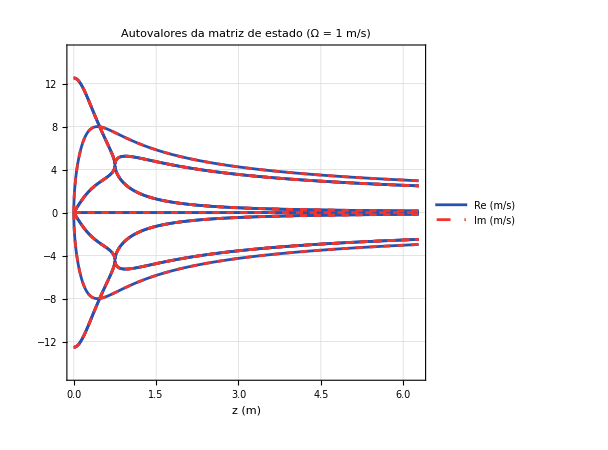

```mathematica
Show[
	Plot[
		Sort@(Re/@Eigenvalues[𝔸/.parsol/.{t->tr}]), {tr,0,2π}, PlotRange->{-15,+15}, 
		PlotStyle->Cool⟦1⟧, GridLines->Automatic, Frame->True, FrameLabel->{"z (m)",None},
		PlotLabel->"Autovalores da matriz de estado \n (Ω = "<> ToString[Ω/.parsol] <>" m/s)",
		PlotLegends->Placed[LineLegend[{"Re (m/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}], Before],
		ImageSize->{450,450},
		AspectRatio->1
		],
	Plot[
		Sort@(*RedundantElim@*)Chop@(Im/@Eigenvalues[𝔸/.parsol/.{t->tr}]),{tr,0,2π}, 
		PlotStyle->{Cool⟦3⟧,Dashed},
		PlotLegends-> Placed[LineLegend[{"Im (m/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}],Before]
		]
	]
```

## COMPARAÇÃO DO MODELO NÃO LINEAR COM LINEAR

### CRIAÇÃO DE (y = C x + D u)

```mathematica
est[t_]= Join[#, D[#,t]]& @({x[t],y[t],z[t],ϕ[t],θ[t],ψ[t]});(*Vetor de estados*)
ent[t_]=u[t];(*Vetor de entradas*)
Subscript[y, 0]=F/.d[t];
Subscript[F, lin]=Subscript[y, 0]+ℂ.est[t](*+𝔻.ent[t]*);
Dimensions[Subscript[F, lin]]
MatrixForm[est[t]]
```

{6,1}

(x[t]
y[t]
z[t]
ϕ[t]
θ[t]
ψ[t]
x'[t]
y'[t]
z'[t]
ϕ'[t]
θ'[t]
ψ'[t])

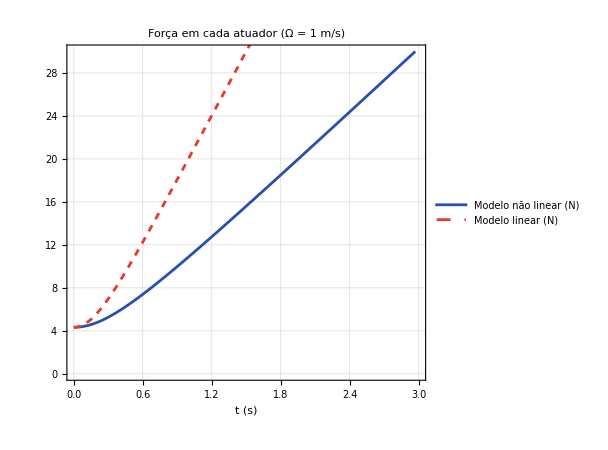

```mathematica
Show[
	Plot[
		F[[1]]/.d[t]/.parsol/.{t->tr}, {tr,0,3}, PlotRange->{-0,+30}, 
		PlotStyle->Cool⟦1⟧, GridLines->Automatic, Frame->True, FrameLabel->{"t (s)",None},
		PlotLabel->"Força em cada atuador \n (Ω = "<> ToString[Ω/.parsol] <>" m/s)",
		PlotLegends->Placed[LineLegend[{"Modelo não linear (N)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}], Before],
		ImageSize->{450,450},
		AspectRatio->1
		],
	Plot[
		Subscript[F, lin][[1]]/.d[t]/.parsol/.{t->tr},{tr,0,3}, 
		PlotStyle->{Cool⟦3⟧,Dashed},
		PlotLegends-> Placed[LineLegend[{"Modelo linear (N)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Roboto",FontSize->16}],Before]
		]
	]
```